## NumericalSim. Phase Sensitivity in SU(1,1) With Loss Modeling

## Step-1: Clear everything and make assumptions:

```mathematica
Clear["Global`*"];
```

```mathematica
assumpt:={T ∈ Reals, T≥ 0,α1 ∈ Reals,α2 ∈ Reals,α1>0,α2>0,g>0,g ∈ Reals,x1 ∈ Reals,x2 ∈ Reals,p1 ∈ Reals,p2 ∈ Reals,nBarTherm ∈ Reals,nBarTherm ≥ 0,r ∈ Reals,r ≥ 0,θ ∈ Reals,0≤θ≤2π,ϕ ∈ Reals,0≤ϕ≤2π,α∈Reals,α≥0,η∈Reals,0<=η≤1};
Refine[ReIm[g],assumpt](*Check if the assumpt is working properly !!*)
```

{g,0}

## Step-2: Execute the function library:

```mathematica
cohMean[α_,θ_]:=Sqrt[2]*α*{Cos[θ],Sin[θ]};
cohCov:=IdentityMatrix[{2,2}];

vacMean:={0,0};
vacCov:=IdentityMatrix[{2,2}];

sqzMean:={0,0};
sqzCov[r_]:={{Cosh[2*r]+Sinh[2*r],0},{0,Cosh[2*r]-Sinh[2*r]}};

thermMean={0,0};
thermCov[nBarTherm_]:=(2*nBarTherm+1)*IdentityMatrix[{2,2}];

dispSqzMean[α_,θ_]:=Sqrt[2]*α*{Cos[θ],Sin[θ]};
dispSqzCov[r_]:={{(Cosh[r]+Sinh[r])^2,0},{0,(Cosh[r]-Sinh[r])^2}};

Subscript[phaseShifter, i_][modeCt_,ϕ_]:=Module[{matrix},
	matrix=IdentityMatrix[2 modeCt];
	Do[
		matrix⟦2i-2+x⟧⟦2i-2+x⟧=Cos[ϕ];
	,{x,1,2}];
	matrix⟦2i⟧⟦2i-1⟧=Sin[ϕ];
	matrix⟦2i-1⟧⟦2i⟧=-Sin[ϕ];
	matrix
];

BS4[T_]:=({{√T, 0, 0, 0, √(1-T), 0, 0, 0}, {0, √T, 0, 0, 0, √(1-T), 0, 0}, {0, 0, √T, 0, 0, 0, √(1-T), 0}, {0, 0, 0, √T, 0, 0, 0, √(1-T)}, {√(1-T), 0, 0, 0, -√T, 0, 0, 0}, {0, √(1-T), 0, 0, 0, -√T, 0, 0}, {0, 0, √(1-T), 0, 0, 0, -√T, 0}, {0, 0, 0, √(1-T), 0, 0, 0, -√T}});



TMSQZ1[rPump_,θPump_]:={{Cosh[rPump],0,Sinh[rPump]Cos[θPump],Sinh[rPump]Sin[θPump]},
						{0,Cosh[rPump],Sinh[rPump]Sin[θPump],-Sinh[rPump] Cos[θPump]},
						{Sinh[rPump]Cos[θPump],Sinh[rPump]Sin[θPump],Cosh[rPump],0},
						{Sinh[rPump]Sin[θPump],-Sinh[rPump] Cos[θPump],0,Cosh[rPump]}};
						
						
						
getWignerFun[outMean_,outCovariance_,quad_,assumpt_,modeCt_]:=Module[{tempc,tempr,wigDenom,wigExponent,wignerFunct},
tempc = (quad-outMean)(*A column vector*);
tempr = ArrayReshape[(quad-outMean),{2*modeCt,1}]ᵀ(*A row vector*);

wigDenom = FullSimplify[π^modeCt*Sqrt[Det[outCovariance]],TimeConstraint->0.5];
wigDenom=Refine[wigDenom,assumpt];

wigExponent = FullSimplify[tempr.Inverse[outCovariance].tempc,TimeConstraint->0.5];
wigExponent=Refine[wigExponent,assumpt];

wignerFunct = FullSimplify[Exp[-wigExponent]/wigDenom,TimeConstraint->0.5];
wignerFunct
];



getWignerFunRaw[outMean_,outCovariance_,quad_,assumpt_,modeCt_]:=Module[{tempc,tempr,wigDenom,wigExponent,wignerFunct},
tempc = (quad-outMean)(*A column vector*);
tempr = ArrayReshape[(quad-outMean),{2*modeCt,1}]ᵀ(*A row vector*);

wigDenom = π^modeCt*Sqrt[Det[outCovariance]];
wigDenom = Refine[wigDenom,assumpt];

wigExponent = tempr.Inverse[outCovariance].tempc;
wigExponent = Refine[wigExponent,assumpt];

wignerFunct = Exp[-wigExponent]/wigDenom;
wignerFunct
];


(*getPhaseSenWithLoss[Xin,Γin,S,gVal,Tval,α1Val,α2Val,rVal,assumpt]*)

getPhaseSenWithLoss[XinVal_,ΓinVal_,SVal_,assumpt_]:=Module[{X2,Γ2,outMeanLowerArm,outCovLowerArm,quadratureLower,wignerLowerArm,modeCtLowerArm,parityLowerArm,delParityLowerArm,derivParityLowerArm,lowerArmDelPhi,sen},
	(*Evolve mean and covariance*)
	X2=Simplify[N[(SVal.XinVal)]](*output mean*);
	Γ2=Simplify[N[(SVal.ΓinVal.Transpose[SVal])]](*output covariance*);
	
	(*get lower arm wigner function*)
	modeCtLowerArm=1;
	MatrixForm[outMeanLowerArm={X2[[3]],X2[[4]]}](*mean at detector B*);
	MatrixForm[outCovLowerArm ={{Γ2[[3,3]],Γ2[[3,4]]},{Γ2[[4,3]],Γ2[[4,4]]}}] (*Covariance matrix at detector B*);
	quadratureLower={quadrature[[3]],quadrature[[4]]};
	wignerLowerArm=getWignerFunRaw[outMeanLowerArm,outCovLowerArm,quadratureLower,assumpt,modeCtLowerArm];
	
	
	parityLowerArm=N[Flatten[π*wignerLowerArm/.{x2-> 0,p2-> 0}]];
	parityLowerArm=FullSimplify[Refine[parityLowerArm,assumpt],TimeConstraint->0.5];
	delParityLowerArm=Sqrt[1-parityLowerArm^2];
	derivParityLowerArm=D[parityLowerArm,ϕ](*this is denominator*)(*I have removed Abs here !!!!!!!!*);
	lowerArmDelPhi=(delParityLowerArm/derivParityLowerArm);
	sen=Limit[lowerArmDelPhi,ϕ->0];
	sen
];


evaluateAndCall[Tval_,gVal_,αVal_,α1Val_,α2Val_,rVal_]:=Module[{XinVal,ΓinVal,SVal,sen},
	MatrixForm[XinVal=FullSimplify[N[Xin/.{g-> gVal,T->Tval,α->αVal,α1->α1Val,α2-> α2Val,r-> rVal}]]];
	MatrixForm[ΓinVal=FullSimplify[N[Γin/.{g-> gVal,T->Tval,α->αVal,α1->α1Val,α2-> α2Val,r-> rVal}]]];
	MatrixForm[SVal=FullSimplify[N[S/.{g-> gVal,T->Tval,α->αVal,α1->α1Val,α2-> α2Val,r-> rVal}]]];
	sen=Abs[getPhaseSenWithLoss[XinVal,ΓinVal,SVal,assumpt]]
];
```

## Step-3: Supply the input mean and covariance:

```mathematica
modeCt=4;

means1=cohMean[α1,0];
means2=dispSqzMean[α2,0];
covMat1=cohCov;
covMat2=dispSqzCov[r];
```

## Step-4: Process the inputs and Evolution matrix:

```mathematica
means:=Flatten[{means1,means2}];
MatrixForm[X0=Refine[means,assumpt]]

covMat:=Fold[ArrayFlatten[{{#1,0},{0,#2}}]&,{covMat1,covMat2}];
MatrixForm[Γ0=Refine[covMat,assumpt]]

MatrixForm[Xin=Flatten[{X0,KroneckerProduct[vacMean,vacMean]}]](* (X^*)_in=(Subscript[X, 0],Subscript[X, Th])^T  This is input mean vector which is 1x8*)
MatrixForm[Γin=Fold[ArrayFlatten[{{#1,0},{0,#2}}]&,{Γ0,KroneckerProduct[vacCov,vacCov]}]](*  Γin^*=({{Γin, Subscript[O, 4]}, {Subscript[O, 4], (ΓTh ⊕ ΓTh)}})  *)
MatrixForm[Sϕ = Refine[Subscript[phaseShifter, 1][modeCt,ϕ], assumpt]]
MatrixForm[SOPA1 =Fold[ArrayFlatten[{{#1,0},{0,#2}}]&,{TMSQZ1[g,0],IdentityMatrix[{4,4}]}]](*first OPA*)(*Subscript[S, OPA]^*=({{Subscript[S, OPA], Subscript[O, 4]}, {Subscript[O, 4], Subscript[I, 4]}})*)
MatrixForm[SOPA2 =Fold[ArrayFlatten[{{#1,0},{0,#2}}]&,{TMSQZ1[g,π],IdentityMatrix[{4,4}]}]](*second OPA*)
MatrixForm[lossMat=BS4[T]]
MatrixForm[S = SOPA2.Sϕ.SOPA1.lossMat]
MatrixForm[quadrature={x1,p1,x2,p2}]
```

(√2 α1
0
√2 α2
0)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | (Cosh[r]+Sinh[r])^2 | 0
0 | 0 | 0 | (Cosh[r]-Sinh[r])^2)

(√2 α1
0
√2 α2
0
0
0
0
0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (Cosh[r]+Sinh[r])^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (Cosh[r]-Sinh[r])^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(Cos[ϕ] | -Sin[ϕ] | 0 | 0 | 0 | 0 | 0 | 0
Sin[ϕ] | Cos[ϕ] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(Cosh[g] | 0 | Sinh[g] | 0 | 0 | 0 | 0 | 0
0 | Cosh[g] | 0 | -Sinh[g] | 0 | 0 | 0 | 0
Sinh[g] | 0 | Cosh[g] | 0 | 0 | 0 | 0 | 0
0 | -Sinh[g] | 0 | Cosh[g] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(Cosh[g] | 0 | -Sinh[g] | 0 | 0 | 0 | 0 | 0
0 | Cosh[g] | 0 | Sinh[g] | 0 | 0 | 0 | 0
-Sinh[g] | 0 | Cosh[g] | 0 | 0 | 0 | 0 | 0
0 | Sinh[g] | 0 | Cosh[g] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(√T | 0 | 0 | 0 | √(1-T) | 0 | 0 | 0
0 | √T | 0 | 0 | 0 | √(1-T) | 0 | 0
0 | 0 | √T | 0 | 0 | 0 | √(1-T) | 0
0 | 0 | 0 | √T | 0 | 0 | 0 | √(1-T)
√(1-T) | 0 | 0 | 0 | -√T | 0 | 0 | 0
0 | √(1-T) | 0 | 0 | 0 | -√T | 0 | 0
0 | 0 | √(1-T) | 0 | 0 | 0 | -√T | 0
0 | 0 | 0 | √(1-T) | 0 | 0 | 0 | -√T)

(√T (Cos[ϕ] Cosh[g]^2-Sinh[g]^2) | -√T Cosh[g]^2 Sin[ϕ] | √T (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) | √T Cosh[g] Sin[ϕ] Sinh[g] | √(1-T) (Cos[ϕ] Cosh[g]^2-Sinh[g]^2) | -√(1-T) Cosh[g]^2 Sin[ϕ] | √(1-T) (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) | √(1-T) Cosh[g] Sin[ϕ] Sinh[g]
√T Cosh[g]^2 Sin[ϕ] | √T (Cos[ϕ] Cosh[g]^2-Sinh[g]^2) | √T Cosh[g] Sin[ϕ] Sinh[g] | √T (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) | √(1-T) Cosh[g]^2 Sin[ϕ] | √(1-T) (Cos[ϕ] Cosh[g]^2-Sinh[g]^2) | √(1-T) Cosh[g] Sin[ϕ] Sinh[g] | √(1-T) (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g])
√T (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) | √T Cosh[g] Sin[ϕ] Sinh[g] | √T (Cosh[g]^2-Cos[ϕ] Sinh[g]^2) | -√T Sin[ϕ] Sinh[g]^2 | √(1-T) (Cosh[g] Sinh[g]-Cos[ϕ] Cosh[g] Sinh[g]) | √(1-T) Cosh[g] Sin[ϕ] Sinh[g] | √(1-T) (Cosh[g]^2-Cos[ϕ] Sinh[g]^2) | -√(1-T) Sin[ϕ] Sinh[g]^2
√T Cosh[g] Sin[ϕ] Sinh[g] | √T (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) | √T Sin[ϕ] Sinh[g]^2 | √T (Cosh[g]^2-Cos[ϕ] Sinh[g]^2) | √(1-T) Cosh[g] Sin[ϕ] Sinh[g] | √(1-T) (-Cosh[g] Sinh[g]+Cos[ϕ] Cosh[g] Sinh[g]) | √(1-T) Sin[ϕ] Sinh[g]^2 | √(1-T) (Cosh[g]^2-Cos[ϕ] Sinh[g]^2)
√(1-T) | 0 | 0 | 0 | -√T | 0 | 0 | 0
0 | √(1-T) | 0 | 0 | 0 | -√T | 0 | 0
0 | 0 | √(1-T) | 0 | 0 | 0 | -√T | 0
0 | 0 | 0 | √(1-T) | 0 | 0 | 0 | -√T)

(x1
p1
x2
p2)

## Step-5: Get phase sensitivity numerically using parity detection:

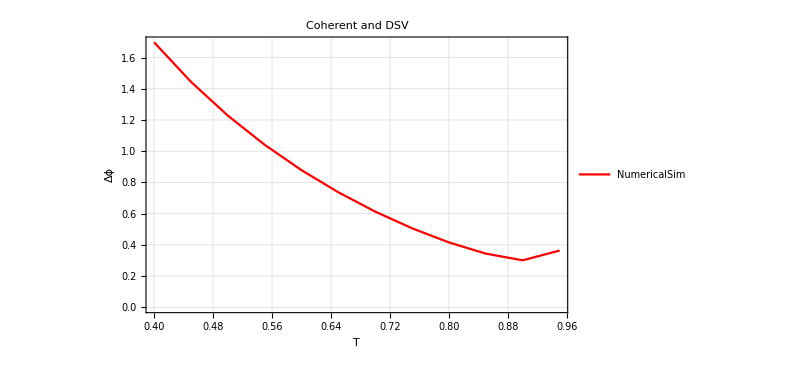

```mathematica
gVal=1;
αVal=4;
α1Val=2;
α2Val=2;
rVal=2;

Tmin=0.4;
Tmax=0.95;
Tstep=0.05;
graphNum=Table[ {Tval, evaluateAndCall[Tval,gVal,αVal,α1Val,α2Val,rVal][[1]]}, {Tval,Tmin,Tmax,Tstep} ];
ListLinePlot[{Abs[graphNum]},PlotStyle->{Red,Dashed,AbsoluteThickness[2]},PlotLabel->"Coherent and DSV",Frame->True,LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"T","Δϕ"},PlotLegends->Placed[{"NumericalSim"},{0.7,0.7}],ImageSize->600,GridLines->Automatic]
```

```mathematica
Tval=0.9;
αVal=4;
α1Val=2;
α2Val=2;
rVal=2;

gmin=0.5;
gmax=3;
gstep=0.1;
graphNum=Table[ {gVal, evaluateAndCall[Tval,gVal,αVal,α1Val,α2Val,rVal][[1]]}, {gVal,gmin,gmax,gstep} ]
ListLinePlot[{Abs[graphNum]},PlotStyle->{Red,Dashed,AbsoluteThickness[2]},PlotLabel->"Coherent and DSV",Frame->True,LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"g","Δϕ"},PlotLegends->Placed[{"NumericalSim"},{0.7,0.7}],ImageSize->600,GridLines->Automatic]
```